Rice, chapter 5: Diffusion Theory
mutation and drift :

```mathematica
ψ[p_,θ_]:=(p(1-p))^(θ-1)
```

```mathematica
θ[Ne_,u_]:= 4*Ne*u
```

```mathematica
Manipulate[Plot[ψ[p,θ],{p,0,1}], {θ,0,10}]
```

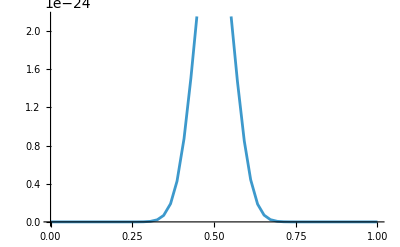

```mathematica
Plot[f[p]=(p-p^2)^(40-1),{p,0,1}]
```

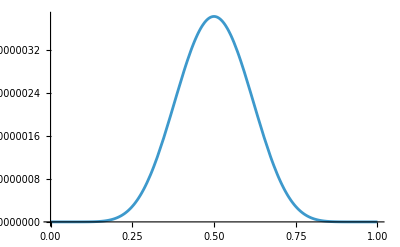

```mathematica
Plot[f[p]=(p-p^2)^(10-1),{p,0,1}]
```

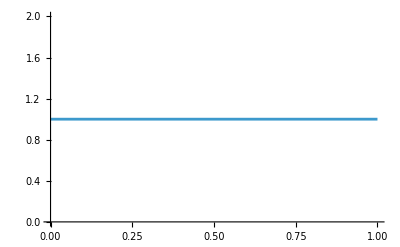

```mathematica
Plot[f[p]=(p-p^2)^(1-1),{p,0,1}]
```

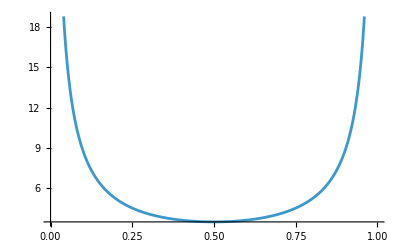

```mathematica
Plot[f[p]=(p-p^2)^(0.1-1),{p,0,1}]
```

```mathematica
Manipulate[Plot[f[p]=(p-p^2)^(θ-1),{p,0,1}], {θ,0,10}]
```

selection and drift:

```mathematica
wbar[p_,w11_,w12_,w22_]:= (p^2)w11 + 2p(1-p)w12 + ((1-p)^2)w22
```

-heterozygote advantage (balancing selection)

```mathematica
Simplify[wbar[p,1,1+s,1]]
```

1+2 p s-2 p^2 s

```mathematica
wbar[p_,s_]:= E^(2s*p(1-p))
```

```mathematica
ψ[p_,Nes_]:=E^(4Nes*p(1-p))/(p(1-p))
```

```mathematica
Manipulate[Plot[ψ[p,Nes],{p,0,1}], {Nes,0,10}]
```

```mathematica
Plot[ψ[p,40],{p,0,1},PlotRange->All]
```

-Graphics-

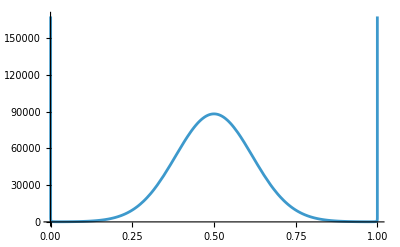

```mathematica
Plot[ψ[p,10],{p,0,1}]
```

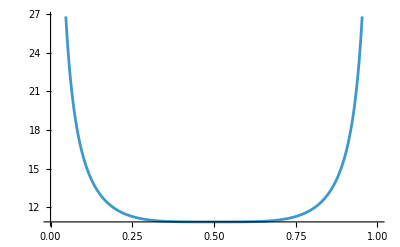

```mathematica
Plot[ψ[p,1],{p,0,1}]
```

- heterozygote intermediate (directional selection)

```mathematica
Simplify[wbar[p,1+2s,1+s,1]]
```

1+2 p s

```mathematica
ψ[p_,Nes_]:=E^(4Nes*p)/(p(1-p))
```

```mathematica
Manipulate[Plot[ψ[p,Nes],{p,0,1}], {Nes,0,10}]
```

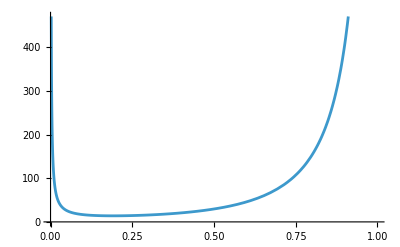

```mathematica
Plot[ψ[p,1],{p,0,1}]
```

```mathematica
Plot[ψ[p,10],{p,0,1}]
```

-Graphics-

```mathematica
Plot[ψ[p,40],{p,0,1}]
```

-Graphics-

mutation, selection, and drift:

```mathematica
Simplify[wbar[p,1-s,1,1]]
```

1-p^2 s

```mathematica
ψ[p_,Ne_,s_,u1_,u2_]:=(E^(-2*Ne*s*(p^2)))*((1-p)^((4*Ne*u1)-1))*(p^((4*Ne*u2)-1))
```

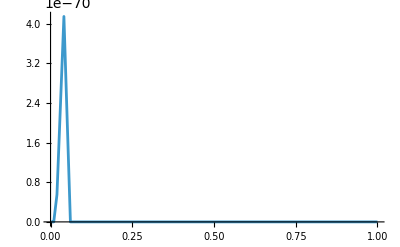

```mathematica
Plot[ψ[p,1000000,0.01,10^(-5),10^(-5)],{p,0,1},PlotRange->All]
```

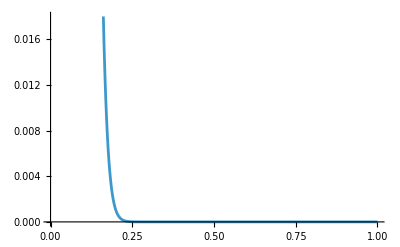

```mathematica
Plot[ψ[p,10000,0.01,10^(-5),10^(-5)],{p,0,1}]
```

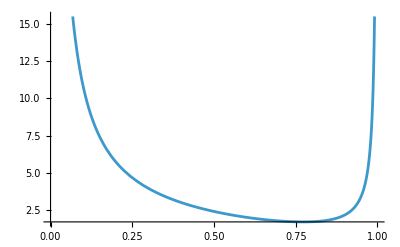

```mathematica
Plot[ψ[p,100,0.01,10^(-5),10^(-5)],{p,0,1}]
```

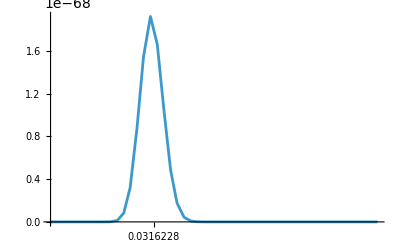

```mathematica
Plot[ψ[p,1000000,0.01,10^(-5),10^(-5)],{p,0,0.1},Ticks->{{Sqrt[10^(-5)/0.01]},Automatic},PlotRange->All]
```

migration between populations:
- migration maintaining variation (neutral allele)

```mathematica
ψ[p_,Nem_]:=(p(1-p))^((2Nem)-1)
```

```mathematica
Manipulate[Plot[ψ[p,Nem],{p,0,1}], {Nem,0,5}]
```

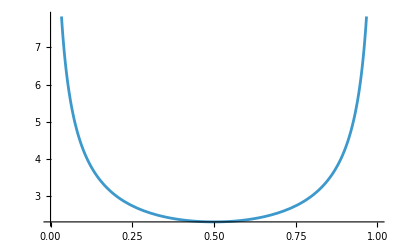

```mathematica
Plot[ψ[p,0.2],{p,0,1}]
```

```mathematica
Plot[ψ[p,0.5],{p,0,1}]
```

-Graphics-

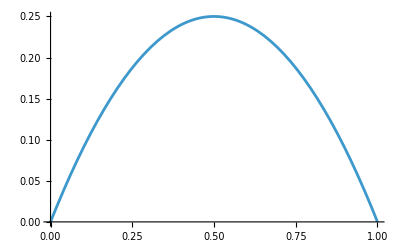

```mathematica
Plot[ψ[p,1],{p,0,1}]
```

```mathematica
Plot[ψ[p,5],{p,0,1}]
```

-Graphics-